## Probability - obtained using Minakata expansion

## Case ϵ_μτ!=0

```mathematica
(* the formula is expanded up to order 3/2 *)

(* In the formula below, we have  *)

(* Δm31 and Δm21 are the mass squared diferences in eV^2 *)

(* ee is the energy in GeV *)

(* dcp is the Dirac CP violation phase *)

(* sij is Sin(Subscript[θ, ij]) and cij is Cos(Subscript[θ, ij]) *)

(* emut is the NSI *)
```

```mathematica
pmut[s12_,c12_,s13_,c13_,s23_,c23_,δ_,dm31_,dm21_,ee_,emut_]=(dm31 (c23^4 ee emut^2 (-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2+dm31^2 (729.-1458. s13^2))+c23^3 ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+148.8066566943162 s13^2)) s23+c23^2 (c12^2 dm21 (-4.5474735088646407*^-13 dm31^2-2.7105054312137608*^-20 ee^2)+ee (1.9999999999999998 dm31^2-0.0008665646560000002 dm31 ee+9.386678787854984*^-8 ee^2+dm31 ((-3.5113576553450443+7.271321001515295*^-17 ⅈ) dm31+2.7105054312137608*^-20 ee+1101.7797307465376 dm31 emut^2) s13^2)) s23^2+c23 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.00000000000001-40.8066566943162 s13^2))) s23^3+ee (729. dm31^2-0.3158628171120001 dm31 ee+0.000034214444181731416 ee^2) emut^2 s23^4)+c23 dm31 (1101.7797307465376 c23^3 dm31^2 ee emut^2 s13^2+c23^2 emut (c12^2 dm21 (-1.455191522836685*^-11 dm31^2-8.6736173798840345*^-19 ee^2)+ee (-0.023397245712 dm31 ee+2.5344032727208456*^-6 ee^2+dm31^2 (54.-135.6133133886324 s13^2))) s23+c23 (c12^2 dm21 (4.5474735088646407*^-13 dm31^2+2.7105054312137608*^-20 ee^2)+ee (ee^2 (-9.386678787854984*^-8+0.00006842888836346283 emut^2)+dm31 ee (0.0008665646560000002-0.6317256342240002 emut^2-2.7105054312137608*^-20 s13^2)+dm31^2 (-1.9999999999999998+3.5113576553450443 s13^2+emut^2 (1458.-1458. s13^2)))) s23^2+ee emut (-2.5344032727208456*^-6 ee^2+dm31 ee (0.023397245712-8.673617379884035*^-19 s13^2)+dm31^2 (-54.+54. s13^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee]+c12 c23 dm21 s12 s13 (-8.673617379884035*^-19 c23^3 dm31 ee^2 emut+c23^2 ((-0.0004332823280000001 dm31+9.386678787854984*^-8 ee) ee^2+(-1.6442870905801747*^6 dm31^3+356.22026925346245 dm31^2 ee+0.31586281711200004 dm31 ee^2-0.00006842888836346282 ee^3) emut^2) s23+c23 (121799.04374667956 dm31^3-26.386686611367594 dm31^2 ee-0.046794491423999995 dm31 ee^2+0.000010137613090883384 ee^3) emut s23^2+(-2255.5378471607337 dm31^3+0.4886423446549555 dm31^2 ee+dm31 ee^2 (0.0004332823280000001-0.3158628171119999 emut^2)+ee^3 (-9.386678787854982*^-8+0.00006842888836346282 emut^2)) s23^3) Cos[(3296.2634783428016 dm31)/ee-1. δ]-0.011698622856 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[δ]+2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[δ]-9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[δ]+2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[δ]+0.0008665646560000002 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[δ]-1.8773357575709967*^-7 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[δ]+1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[δ]-0.9475884513359999 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[δ]+0.00013685777672692564 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[δ]-747780.3248878407 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[δ]+54.00000000000003 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[δ]+0.093588982848 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[δ]-0.000015206419636325076 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[δ]+9231.855862812848 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[δ]-5.551115123125783*^-16 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[δ]-0.0012998469840000003 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[δ]+1.8773357575709967*^-7 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[δ]-1.3460045847981133*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[δ]+2916.000000000001 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[δ]+0.6317256342240001 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[δ]-0.00013685777672692564 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[δ]+249260.10829594688 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[δ]-54.00000000000001 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[δ]+2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[δ]+6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[1. δ]-1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[1. δ]-1458. c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[1. δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[1. δ]+565081.7592678213 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[1. δ]-14.419970082948637 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[1. δ]-0.023397245712 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[1. δ]-6976.318015652115 c12 c23 dm21 dm31^3 s12 s13 s23^3 Cos[1. δ]-0.48864234465495493 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[1. δ]+0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[1. δ]+1.0171471666820783*^7 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Cos[1. δ]-2203.559461493075 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[1. δ]-188360.5864226071 c12 dm21 dm31^3 emut s12 s13 s23^4 Cos[1. δ]+40.80665669431621 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[1. δ]-249260.10829594688 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+54.000000000000014 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+0.011698622856000002 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 c23^4 dm21 ee^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+δ]+9231.855862812848 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-2.000000000000001 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.0004332823280000001 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+9.386678787854984*^-8 c12 c23^3 dm21 ee^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-6.730022923990566*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+1458.0000000000005 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+0.31586281711200004 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]-0.00006842888836346282 c12 c23^3 dm21 ee^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+δ]+249260.10829594696 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-(0.035095868568+1.925929944387236*^-34 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]+5.068806545441692*^-6 c12 c23^2 dm21 ee^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+δ]-1.9999999999999996 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.0008665646560000002 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-9.386678787854982*^-8 c12 c23 dm21 ee^3 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-0.631725634224 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]+0.00006842888836346282 c12 c23 dm21 ee^3 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+δ]-54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+0.023397245712 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]-2.5344032727208456*^-6 c12 dm21 ee^3 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+δ]+188360.5864226071 c12 c23^4 dm21 dm31^3 emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-40.80665669431621 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Cos[(3296.2634783428016 dm31)/ee+1. δ]-6976.318015652115 c12 c23^3 dm21 dm31^3 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.511357655345045 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]+5.085735833410392*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1101.7797307465376 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Cos[(3296.2634783428016 dm31)/ee+1. δ]-188360.5864226071 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]-13.19334330568379 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.011698622856 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Cos[(3296.2634783428016 dm31)/ee+1. δ]+1.9999999999999998 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.0004332823280000001 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]-1458. c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+0.31586281711200004 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Cos[(3296.2634783428016 dm31)/ee+1. δ]+54. c12 dm21 dm31^2 ee emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]-0.011698622856 c12 dm21 dm31 ee^2 emut s12 s13 s23^4 Cos[(3296.2634783428016 dm31)/ee+1. δ]+954.9059770030174 c23^4 dm31^3 ee emut^2 s13^2 Sin[(3296.2634783428016 dm31)/ee]+177998.22783051126 c12^2 c23^3 dm21 dm31^3 emut s23 Sin[(3296.2634783428016 dm31)/ee]-77.12348653427833 c12^2 c23^3 dm21 dm31^2 ee emut s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c12^2 c23^3 dm21 dm31 ee^2 emut s23 Sin[(3296.2634783428016 dm31)/ee]-109.29551934143674 c23^3 dm31^3 ee emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]+0.008354060947262194 c23^3 dm31^2 ee^2 emut s13^2 s23 Sin[(3296.2634783428016 dm31)/ee]-6592.526956685602 c12^2 c23^2 dm21 dm31^3 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.856425427195494 c12^2 c23^2 dm21 dm31^2 ee s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c12^2 c23^2 dm21 dm31 ee^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+4.805952151423804*^6 c12^2 c23^2 dm21 dm31^3 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-2082.334136425515 c12^2 c23^2 dm21 dm31^2 ee emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c12^2 c23^2 dm21 dm31 ee^2 emut^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+2.7380974557143687 c23^2 dm31^3 ee s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-0.0003094096647134146 c23^2 dm31^2 ee^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-1041.1670682127576 c23^2 dm31^3 ee emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]+0.22555964557607924 c23^2 dm31^2 ee^2 emut^2 s13^2 s23^2 Sin[(3296.2634783428016 dm31)/ee]-177998.22783051128 c12^2 c23 dm21 dm31^3 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+77.12348653427834 c12^2 c23 dm21 dm31^2 ee emut s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c12^2 c23 dm21 dm31 ee^2 emut s23^3 Sin[(3296.2634783428016 dm31)/ee]+38.561743267139164 c23 dm31^3 ee emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]-0.008354060947262194 c23 dm31^2 ee^2 emut s13^2 s23^3 Sin[(3296.2634783428016 dm31)/ee]+4.407777171115168*^6 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-954.9059770030176 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee-1. δ]-326502.0126751977 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+70.7337760742976 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee-1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[(3296.2634783428016 dm31)/ee-1. δ]-1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[δ]+4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[δ]-4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[δ]-5.534686227014404*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[δ]+2.3980817331903384*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[δ]-(2.5976160902274616*^-18+1.3877787807814457*^-17 ⅈ) c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[δ]-7.471826406469446*^-10 c12 c23 dm21 dm31^3 emut^2 s12 s13 s23^3 Sin[δ]+3.237410339806957*^-13 c12 c23 dm21 dm31^2 ee emut^2 s12 s13 s23^3 Sin[δ]-3.5067817218070734*^-17 c12 c23 dm21 dm31 ee^2 emut^2 s12 s13 s23^3 Sin[δ]+6046.333568059216 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[1. δ]-1.3098847421166222 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[1. δ]+1.6187051699034782*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[1. δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[1. δ]+163251.00633759884 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[1. δ]-35.3668880371488 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[1. δ]+2.5976160902274616*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[1. δ]+6046.333568059216 c12 c23 dm21 dm31^3 s12 s13 s23^3 Sin[1. δ]-1.3098847421166222 c12 c23 dm21 dm31^2 ee s12 s13 s23^3 Sin[1. δ]-4.8104001670878927*^-20 c12 c23 dm21 dm31 ee^2 s12 s13 s23^3 Sin[1. δ]+163251.00633759884 c12 dm21 dm31^3 emut s12 s13 s23^4 Sin[1. δ]-35.3668880371488 c12 dm21 dm31^2 ee emut s12 s13 s23^4 Sin[1. δ]-2.767343113507202*^-11 c12 c23^4 dm21 dm31^3 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.1990408665951692*^-14 c12 c23^4 dm21 dm31^2 ee emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]-1.2988080451137308*^-18 c12 c23^4 dm21 dm31 ee^2 emut s12 s13 Sin[(3296.2634783428016 dm31)/ee+δ]+1.0249418938915565*^-12 c12 c23^3 dm21 dm31^3 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-4.440892098500627*^-16 c12 c23^3 dm21 dm31^2 ee s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+4.8104001670878927*^-20 c12 c23^3 dm21 dm31 ee^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-7.471826406469446*^-10 c12 c23^3 dm21 dm31^3 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+3.237410339806957*^-13 c12 c23^3 dm21 dm31^2 ee emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]-3.5067817218070734*^-17 c12 c23^3 dm21 dm31 ee^2 emut^2 s12 s13 s23 Sin[(3296.2634783428016 dm31)/ee+δ]+2.767343113507202*^-11 c12 c23^2 dm21 dm31^3 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]-1.1990408665951692*^-14 c12 c23^2 dm21 dm31^2 ee emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+1.2988080451137308*^-18 c12 c23^2 dm21 dm31 ee^2 emut s12 s13 s23^2 Sin[(3296.2634783428016 dm31)/ee+δ]+c12 dm21 dm31 s12 s13 (c23^4 dm31 (163251.00633759884 dm31-35.3668880371488 ee) emut+c23^3 dm31 (-6046.333568059216 dm31+1.3098847421166222 ee+4.407777171115168*^6 dm31 emut^2-954.9059770030176 ee emut^2) s23+c23^2 (-163251.00633759887 dm31^2+35.3668880371488 dm31 ee-1.2988080451137308*^-18 ee^2) emut s23^2+c23 ee (-1.1102230246251565*^-16 dm31+4.8104001670878927*^-20 ee+(1.6187051699034782*^-13 dm31-3.5067817218070734*^-17 ee) emut^2) s23^3+(-5.995204332975845*^-15 dm31+1.2988080451137308*^-18 ee) ee emut s23^4) Sin[(3296.2634783428016 dm31)/ee+1. δ])/(dm31 (dm31-0.00021664116400000005 ee)^2 ee);
```

## Check

```mathematica
(* numeric from 1904.07265 *)
```

```mathematica
repNum=Thread[{s12,s13,s23,dcp,dm21,dm31}->{Sqrt@0.31,Sqrt@0.02240,Sqrt@0.582,-2.5,7.39*10^-5,2.525*10^-3}];
```

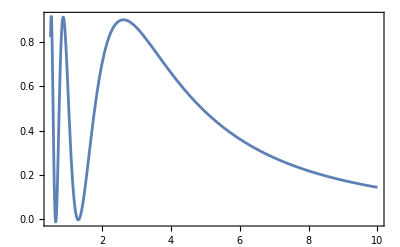

```mathematica
pmut[s12,c12,s13,c13,c23,s23,dcp,dm31,dm21,ee,0]/.Thread[{c12,c13,c23}->{Sqrt[1-s12^2],Sqrt[1-s13^2],Sqrt[1-s23^2]}]/.repNum;
Plot[%,{ee,0.5,10},Frame->True]
```

```mathematica
(* compare with figure 4 of 1904.07265 *)
```